# xTerior: exterior calculus in the Wolfram language

## Exterior calculus has many applications in Mathematics & Physics:

Stokes theorem (fundamental theorem of calculus in any dimension).

Topology: de Rham theorem.

Cartan structure equations.

Gauge theories in physics.

## Contents

### 1st part: differential forms in coordinates.

xTerior and its relation to xAct.

A very simple session with xTerior.

Coordinate changes of differential forms and pull-back. Use for the integration of differential forms.

Finding a local potential for a closed differential form.

Hodge dual and co-differential.

Divergence, curl in terms of differential forms.

### 2nd part: tensor valued differential forms.

Working with tensor valued forms.

Cartan structure equations.

Example: Chern-Simons forms.

Example: Einstein-Cartan theory.

## The xAct project

12 years of development.

500+ different commands and 35000 lines of Wolfram language code.

170+ scientific papers using xAct.

1500+ posts in the xAct forum.

See www.xact.es

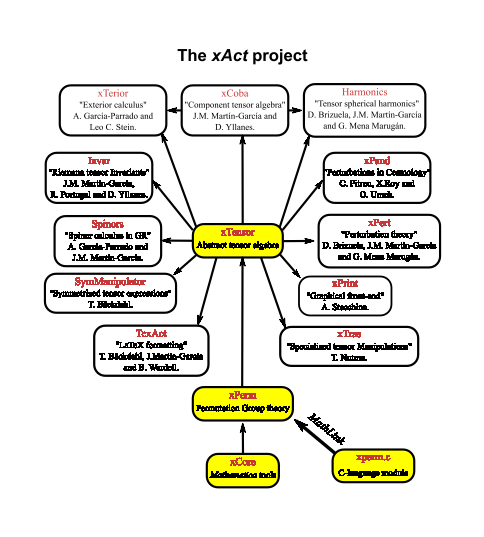

## Sample session in xTerior

We load xTerior. All necessary xAct packages are automatically loaded.

```mathematica
<<xAct`xTerior`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.1, {2014,2,15}

CopyRight (C) 2003-2014, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.1, {2014,9,28}

CopyRight (C) 2002-2014, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.2, {2014,9,28}

CopyRight (C) 2005-2014, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xTerior`  version 0.8.5, {2013,7,1}

CopyRight (C) 2013, Alfonso Garcia-Parrado Gomez-Lobo and Leo C. Stein, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

We remove unnecessary info messages:

```mathematica
$DefInfoQ=False;
$UndefInfoQ=False;
```

```mathematica
$CVVerbose=False;
```

We declare a 3-dimensional coordinate system, with coordinates {x, y, z}. For that we use xAct Def commands to declare a manifold and a coordinate chart.

```mathematica
DefManifold[M3,3,{a,b,c,d,f,g}]
DefChart[Ec,M3,{1,2,3},{x[],y[],z[]}]
```

We are now able to work with arbitrary differential forms written in these coordinates. They are all combinations of the wedge product of coordinate differentials:

```mathematica
Diff[x[]]⋀Diff[y[]]
```

d[x]⋀d[y]

Wedge product is the Wolfram language built-in symbol Wedge, entered with Esc ^ Esc. All differential forms in these coordinates can be written as combinations of elements in the following list.

```mathematica
{Diff[x[]],Diff[y[]],Diff[z[]],Diff[x[]]⋀Diff[y[]],Diff[x[]]⋀Diff[z[]],Diff[y[]]⋀Diff[z[]],Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]}
```

{d[x],d[y],d[z],d[x]⋀d[y],d[x]⋀d[z],d[y]⋀d[z],d[x]⋀d[y]⋀d[z]}

## Basic operations

We can represent any differential form, and do operations on it.

```mathematica
ω=(x[]^2+y[]^2)Diff[z[]]⋀Diff[x[]]-1/(x[]^2+y[]^2)Diff[x[]]⋀Diff[y[]]
```

-(d[x]⋀d[y])/(x^2+y^2)+d[z]⋀d[x] (x^2+y^2)

```mathematica
ω⋀Diff[z[]]
```

-(d[x]⋀d[y]⋀d[z])/(x^2+y^2)+d[z]⋀d[x]⋀d[z] (x^2+y^2)

The Simplification command takes into account the wedge product and its special properties.

```mathematica
?Simplification
```

Simplification[expr] simplifies expr by calling Simplify[ ToCanonical[expr] ].

```mathematica
Simplification@%%
```

-(d[x]⋀d[y]⋀d[z])/(x^2+y^2)

The degree of  a differential form is obtained with Deg:

```mathematica
Deg@%
```

3

The exterior derivative and its properties are implemented by means of the action of  Diff.

```mathematica
Diff@ω
```

2 d[x]⋀d[z]⋀d[x] x+2 d[y]⋀d[z]⋀d[x] y+(2 d[x]⋀d[x]⋀d[y] x+2 d[y]⋀d[x]⋀d[y] y)/((x^2+y^2)^2)

```mathematica
Simplification@%
```

2 d[x]⋀d[y]⋀d[z] y

We can also work with general differential forms written in the coordinates {x,y,z}. For example, let us declare a set of scalar functions:

```mathematica
DefScalarFunction/@{Fx,Fy,Fz};
PrintAs@Fx^="F_x";PrintAs@Fy^="F_y";PrintAs@Fz^="F_z";
```

A scalar function is a head that can take as its arguments any number of coordinates:

```mathematica
{Fx[x[]],Fx[x[],x[]],Fx[x[],y[],z[]]}
```

{F_x[x],F_x[x,x],F_x[x,y,z]}

We can use the scalar functions to represent a generic 2-form and do operations on it:

```mathematica
ψ=Fx[x[],y[],z[]]Diff[y[]]⋀Diff[z[]]-Fy[x[],y[],z[]]Diff[x[]]⋀Diff[z[]]+Fz[x[],y[],z[]]Diff[x[]]⋀Diff[y[]]
```

F_z[x,y,z] d[x]⋀d[y]-F_y[x,y,z] d[x]⋀d[z]+F_x[x,y,z] d[y]⋀d[z]

```mathematica
Diff@ψ//Simplification
```

d[x]⋀d[y]⋀d[z] (F_z^(0,0,1)[x,y,z]+F_y^(0,1,0)[x,y,z]+F_x^(1,0,0)[x,y,z])

As is well-known the double exterior derivative is zero. Hence the double action of Diff yields zero

```mathematica
Diff@%//Simplification
```

0

More examples:

```mathematica
φ=Fx[x[],y[],z[]]Diff@x[]+Fy[x[],y[],z[]]Diff@y[]+Fz[x[],y[],z[]]Diff@z[]
```

d[x] F_x[x,y,z]+d[y] F_y[x,y,z]+d[z] F_z[x,y,z]

```mathematica
dφ=Diff@φ//Simplification
```

d[y]⋀d[z] (-F_y^(0,0,1)[x,y,z]+F_z^(0,1,0)[x,y,z])+d[x]⋀d[y] (-F_x^(0,1,0)[x,y,z]+F_y^(1,0,0)[x,y,z])+d[x]⋀d[z] (-F_x^(0,0,1)[x,y,z]+F_z^(1,0,0)[x,y,z])

We check that the previous expression is essentially the curl of the vector field {Fx,Fy,Fz} when regarded as a field in the Euclidean 3-space.

```mathematica
Curl[{Fx[x[],y[],z[]],Fy[x[],y[],z[]],Fz[x[],y[],z[]]},{x[],y[],z[]}]
```

{-F_y^(0,0,1)[x,y,z]+F_z^(0,1,0)[x,y,z],F_x^(0,0,1)[x,y,z]-F_z^(1,0,0)[x,y,z],-F_x^(0,1,0)[x,y,z]+F_y^(1,0,0)[x,y,z]}

And this is the divergence

```mathematica
ψ
```

F_z[x,y,z] d[x]⋀d[y]-F_y[x,y,z] d[x]⋀d[z]+F_x[x,y,z] d[y]⋀d[z]

```mathematica
Coefficient[Diff@ψ//Simplification,Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]]
```

F_z^(0,0,1)[x,y,z]+F_y^(0,1,0)[x,y,z]+F_x^(1,0,0)[x,y,z]

```mathematica
Div[{Fx[x[],y[],z[]],Fy[x[],y[],z[]],Fz[x[],y[],z[]]},{x[],y[],z[]}]
```

F_z^(0,0,1)[x,y,z]+F_y^(0,1,0)[x,y,z]+F_x^(1,0,0)[x,y,z]

## Change of coordinates

Let us introduce a new coordinate system

```mathematica
DefChart[Sp,M3,{1,2,3},{r[],θ[],ζ[]}]
```

The relation between the new and the old coordinates is

```mathematica
EcToSp={x[]->r[]Sin[θ[]]Cos[ζ[]],y[]->r[]Sin[θ[]]Sin[ζ[]],z[]->r[]Cos[θ[]]}
```

{x→Cos[ζ] r Sin[θ],y→r Sin[ζ] Sin[θ],z→Cos[θ] r}

This enables us to write any differential form in the new coordinates. For example:

```mathematica
ω
```

-(d[x]⋀d[y])/(x^2+y^2)+d[z]⋀d[x] (x^2+y^2)

```mathematica
ω/.EcToSp
```

-((Cos[ζ] Sin[ζ] Sin[θ]^2 d[r]⋀d[r]+Cos[ζ]^2 r Sin[θ]^2 d[r]⋀d[ζ]+Cos[ζ] Cos[θ] r Sin[ζ] Sin[θ] d[r]⋀d[θ]-r Sin[ζ]^2 Sin[θ]^2 d[ζ]⋀d[r]-Cos[ζ] r^2 Sin[ζ] Sin[θ]^2 d[ζ]⋀d[ζ]-Cos[θ] r^2 Sin[ζ]^2 Sin[θ] d[ζ]⋀d[θ]+Cos[ζ] Cos[θ] r Sin[ζ] Sin[θ] d[θ]⋀d[r]+Cos[ζ]^2 Cos[θ] r^2 Sin[θ] d[θ]⋀d[ζ]+Cos[ζ] Cos[θ]^2 r^2 Sin[ζ] d[θ]⋀d[θ])/(Cos[ζ]^2 r^2 Sin[θ]^2+r^2 Sin[ζ]^2 Sin[θ]^2))+(Cos[ζ]^2 r^2 Sin[θ]^2+r^2 Sin[ζ]^2 Sin[θ]^2) (Cos[ζ] Cos[θ] Sin[θ] d[r]⋀d[r]-Cos[θ] r Sin[ζ] Sin[θ] d[r]⋀d[ζ]+Cos[ζ] Cos[θ]^2 r d[r]⋀d[θ]-Cos[ζ] r Sin[θ]^2 d[θ]⋀d[r]+r^2 Sin[ζ] Sin[θ]^2 d[θ]⋀d[ζ]-Cos[ζ] Cos[θ] r^2 Sin[θ] d[θ]⋀d[θ])

```mathematica
Simplification@%
```

1/r(-(1+Cos[ζ]^2 Cos[θ] r^4 Sin[ζ] Sin[θ]^3+Cos[θ] r^4 Sin[ζ]^3 Sin[θ]^3) d[r]⋀d[ζ]+Cos[ζ] r^4 Sin[θ]^2 d[r]⋀d[θ]+r (Cot[θ]-r^4 Sin[ζ] Sin[θ]^4) d[ζ]⋀d[θ])

```mathematica
Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]
```

d[x]⋀d[y]⋀d[z]

```mathematica
%/.EcToSp//Simplification
```

-r^2 Sin[θ] d[r]⋀d[ζ]⋀d[θ]

The change of coordinates enables us to integrate differential forms over regions: For example take the 2-form

```mathematica
(x[]^2+y[]^2+z[]^2)^(-3/2)(z[]Diff@x[]⋀Diff@y[]-y[]Diff@x[]⋀Diff@z[]+x[]Diff@y[]⋀Diff@z[])
```

(d[y]⋀d[z] x-d[x]⋀d[z] y+d[x]⋀d[y] z)/((x^2+y^2+z^2)^(3/2))

Let us integrate this 2-form over the unit 2-dim sphere: first we write the form in spherical coordinates:

```mathematica
%/.EcToSp//Simplification//PowerExpand
```

-Sin[θ] d[ζ]⋀d[θ]

Next we integrate:

```mathematica
Integrate[%/._Wedge->1,{θ[],0,Pi},{ζ[],0,2Pi}]
```

-4 π

## Find a potential

If ω is a p-form and dω = 0 on an open star-shaped set 𝒰 with respect to a point a, then there exists a p-1 form ϕ on 𝒰 such that 
dϕ =ω (Poincaré Lemma).

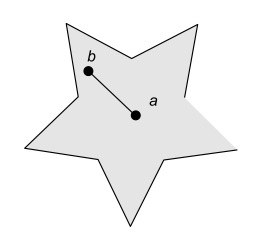

We can attempt to find the form ϕ with the command FindPotential.

```mathematica
?FindPotential
```

FindPotential[form, point, chart] uses the Poincaré lemma to compute a potential for a closed form form (no checks are carried out to ensure that the form is actually closed). The form must be written in some explicit coordinates belonging to chart and the argument point is the point, assumed to be in the same coordinate chart as form, which defines a star-shaped region where the potential is differentiable. A change in the point will give in general a different potential

Any 3-form is closed

```mathematica
η=Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]
```

d[x]⋀d[y]⋀d[z]

A local potential with ℝ^3as the star-shaped set and the origin {0,0,0} as the reference point.

```mathematica
FindPotential[η,{0,0,0},Ec]
```

1/3 d[y]⋀d[z] x-1/3 d[x]⋀d[z] y+1/3 d[x]⋀d[y] z

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z]

Another potential with another point as the reference

```mathematica
FindPotential[η,{1,1,1},Ec]//Simplification
```

1/3 (d[y]⋀d[z] (-1+x)-d[x]⋀d[z] (-1+y)+d[x]⋀d[y] (-1+z))

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z]

A more involved example: take the 3-form:

```mathematica
Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]y[]
```

d[x]⋀d[y]⋀d[z] y

Again it is closed. Let us find a pontential

```mathematica
FindPotential[%,{0,0,0},Ec]
```

1/4 d[y]⋀d[z] x y-1/4 d[x]⋀d[z] y^2+1/4 d[x]⋀d[y] y z

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z] y

For any other differential form μ, not necessarly exact, the following identity holds

```mathematica
identityForms=μ==Diff@FindPotential[μ,p0,Coord1]+FindPotential[Diff@μ,p0,Coord1];
```

Where p0 and Coord1 are an arbitrary point and arbitrary coordinate system : let us check the identity in a particular case :

```mathematica
μ=-(x[]^2+y[]^2)Diff[x[]]⋀Diff[y[]]+Diff[z[]]⋀Diff[x[]](x[]^2-y[]^2)
```

d[x]⋀d[y] (-x^2-y^2)+d[z]⋀d[x] (x^2-y^2)

```mathematica
identityForms/.{Coord1->Ec,p0->{1,1,1}}
```

d[x]⋀d[y] (-x^2-y^2)+d[z]⋀d[x] (x^2-y^2)==-1/6 d[x]⋀d[x] (1+3 x) (-1+y)-1/6 (-(d[y]⋀d[y]) (-1+x)+d[x]⋀d[y] (-1+y)+d[y]⋀d[x] (-1+y)) (1+3 y)+1/12 (2 d[x]⋀d[y] (1-x)+2 d[y]⋀d[y] (1-x)+6 d[x]⋀d[y] (1-x) x+2 d[x]⋀d[x] (-1+y)+2 d[y]⋀d[x] (-1+y)+6 d[x]⋀d[x] x (-1+y)+6 d[y]⋀d[y] (1-x) y+6 d[y]⋀d[x] (-1+y) y+(-(d[x]⋀d[y])+d[y]⋀d[x]) (2+2 x+3 x^2+2 y+3 y^2))+1/12 ((-(d[x]⋀d[z])+d[z]⋀d[x]) (x-y) (2+3 x+3 y)+(2+3 x+3 y) (d[x]⋀d[z] (1-x)-d[y]⋀d[z] (1-x)+d[x]⋀d[x] (-1+z)-d[y]⋀d[x] (-1+z))+(x-y) (3 d[x]⋀d[z] (1-x)+3 d[y]⋀d[z] (1-x)+3 d[x]⋀d[x] (-1+z)+3 d[y]⋀d[x] (-1+z)))+1/6 (1+3 x) ((d[x]⋀d[z]+d[z]⋀d[x]) (-1+x)-d[x]⋀d[x] (-1+z))-1/6 (1+3 y) (d[y]⋀d[z] (-1+x)+d[z]⋀d[x] (-1+y)-d[y]⋀d[x] (-1+z))

```mathematica
Simplification@%
```

True

## Hodge dual and codifferential

If we introduce a metric in a manifold ℳ of dimension n then we can define on the set Λ(ℳ) (differentiable forms on ℳ) the Hodge operator ⋆ and the co-differential δ :
⋆ : Λ^p(ℳ)→Λ^(n-p)(ℳ)
δ :  Λ^p(ℳ)→Λ^(p-1)(ℳ), δ≡(-1)^(n(p+1)+s)⋆ d ⋆
To compute these operators in xTerior one uses ExpandHodgeDual and CodiffToDiff respectively

We need to associate a metric to the coordinates we are working with. In this example, we shall take a coordinate system predefined in Mathematica.

```mathematica
DefChart[Cyl,M3,{1,2,3},{ρ[],θ[],ζ[]}]
```

The components of the metric tensor are given by

```mathematica
metricCyl=CoordinateChartData["Cylindrical","Metric"][{ρ[],θ[],ζ[]}]
```

{{1,0,0},{0,ρ^2,0},{0,0,1}}

In order that xTerior recognizes this as the metric in cylindrical coordinates one has to wrap it with the CTensor head as follows:

```mathematica
metricCyl=CTensor[metricCyl,{-Cyl,-Cyl}]
```

CTensor[{{1,0,0},{0,ρ^2,0},{0,0,1}},{-Cyl,-Cyl},0]

```mathematica
SetCMetric[metricCyl,Cyl,SignatureOfMetric->{3,0,0}]
```

Once this is done we can compute the Hodge dual and the co-differential of any form in the given coordinates.  For example:

```mathematica
Diff[ρ[]]
```

d[ρ]

```mathematica
Hodge[metricCyl]@%
```

*[d[ρ]]

The actual computation of the Hodge dual is carried out with ExpandHodgeDual as follows:

```mathematica
ToValues@ExpandHodgeDual[%,dx[M3],metricCyl]
```

d[θ]⋀d[ζ] √(ρ^2)

```mathematica
%//PowerExpand
```

d[θ]⋀d[ζ] ρ

We can use these feature to compute the Hodge Laplacian.

```mathematica
DefScalarFunction[Φ]
```

Forms of degree higher than the dimension will be set to zero automatically.

```mathematica
UseDimensionStart[]
```

The Hodge laplacian acting on any form ω is defined by dδ ω +δ d ω.  In this case we take ω = ϕ

```mathematica
Codiff[metricCyl]@Diff@Φ[ρ[],θ[],ζ[]]+Diff@Codiff[metricCyl]@Φ[ρ[],θ[],ζ[]]
```

d[δ[Φ[ρ,θ,ζ]]]+δ[d[ζ] Φ^(0,0,1)[ρ,θ,ζ]]+δ[d[θ] Φ^(0,1,0)[ρ,θ,ζ]]+δ[d[ρ] Φ^(1,0,0)[ρ,θ,ζ]]

```mathematica
CodiffToDiff@%
```

(*[d[*[d[ζ]]]]) Φ^(0,0,1)[ρ,θ,ζ]+(*[d[ζ]⋀(*[d[ζ]])]) Φ^(0,0,2)[ρ,θ,ζ]+(*[d[*[d[θ]]]]) Φ^(0,1,0)[ρ,θ,ζ]+(*[d[ζ]⋀(*[d[θ]])]) Φ^(0,1,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[d[ζ]])]) Φ^(0,1,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[d[θ]])]) Φ^(0,2,0)[ρ,θ,ζ]+(*[d[*[d[ρ]]]]) Φ^(1,0,0)[ρ,θ,ζ]+(*[d[ζ]⋀(*[d[ρ]])]) Φ^(1,0,1)[ρ,θ,ζ]+(*[d[ρ]⋀(*[d[ζ]])]) Φ^(1,0,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[d[ρ]])]) Φ^(1,1,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[d[θ]])]) Φ^(1,1,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[d[ρ]])]) Φ^(2,0,0)[ρ,θ,ζ]

We work out the exterior derivative and the Hodge duals

```mathematica
ExpandHodgeDual[%,dx[M3],metricCyl];
```

```mathematica
ExpandHodgeDual[%,dx[M3],metricCyl]
```

Φ^(0,0,2)[ρ,θ,ζ]+(Φ^(0,2,0)[ρ,θ,ζ])/ρ^2+(Φ^(1,0,0)[ρ,θ,ζ])/ρ+Φ^(2,0,0)[ρ,θ,ζ]

Compare with Mathematica.

```mathematica
Laplacian[Φ[ρ[],θ[],ζ[]],{ρ[],θ[],ζ[]},"Cylindrical"]//Expand
```

Φ^(0,0,2)[ρ,θ,ζ]+(Φ^(0,2,0)[ρ,θ,ζ])/ρ^2+(Φ^(1,0,0)[ρ,θ,ζ])/ρ+Φ^(2,0,0)[ρ,θ,ζ]

```mathematica
UnsetCMetric@metricCyl
```

## Div and Curl in terms of differential forms

Let F be a vector field in ℝ^3. Then we have the following relations
∇·F ⟺ δ F, if F is regarded as a 1-form in ℝ^3.
∇×F ⟺ ⋆ d F, if F is regarded as a 1-form in ℝ^3.
 F  is a 1-form in ℝ^3 ⟹ F=F_1 θ^1+F_2 θ^2+F_3 θ^3
 {θ^1,θ^2,θ^3} is an orthonormal co-base in ℝ^3 with respect to a chosen metric g.

For this we need to define first an orthonormal frame. The orthonormal frame is related to the original cylindrical coordinates by means of the following change of frame matrix:

```mathematica
ChangeFrame={{1,0,0},{0,ρ[],0},{0,0,1}};
```

```mathematica
%//MatrixForm
```

(1 | 0 | 0
0 | ρ | 0
0 | 0 | 1)

Definition of the actual orthonormal frame called frame. Note that we need to specify the relation between frame and  the old coordinate chart called Cyl at definition time.

```mathematica
DefBasis[frame,TangentM3,{1,2,3},BasisColor->RGBColor[0,0,1],BasisChange->CTensor[Inverse@ChangeFrame,{-frame,Cyl}]]
```

In this frame the metric tensor takes the diagonal form.

```mathematica
metricframe=CTensor[DiagonalMatrix[{1,1,1}],{-frame,-frame}]
```

CTensor[{{1,0,0},{0,1,0},{0,0,1}},{-frame,-frame},0]

We set now this metric as the metric with which we are going to do computations.

```mathematica
SetCMetric[metricframe,Cyl,SignatureOfMetric->{3,0,0}]
```

Set of orthonormal 1-forms with respect to the defined metric:

```mathematica
{Coframe[M3][{1,frame}],Coframe[M3][{2,frame}],Coframe[M3][{3,frame}]}
```

{θ | 1
 ,θ | 2
 ,θ | 3
 }

Relation between the orthonormal co-base and the holonomic co-base.

```mathematica
dx[M3][{a,Cyl}]==TraceBasisDummy[Basis[-{b,frame},{a,Cyl}]Coframe[M3][{b,frame}]]
```

dx | a
 ==e |   | a
1 |   θ | 1
 +e |   | a
2 |   θ | 2
 +e |   | a
3 |   θ | 3

```mathematica
ComponentArray@%
```

{dx | 1
 ==e |   | 1
1 |   θ | 1
 +e |   | 1
2 |   θ | 2
 +e |   | 1
3 |   θ | 3
 ,dx | 2
 ==e |   | 2
1 |   θ | 1
 +e |   | 2
2 |   θ | 2
 +e |   | 2
3 |   θ | 3
 ,dx | 3
 ==e |   | 3
1 |   θ | 1
 +e |   | 3
2 |   θ | 2
 +e |   | 3
3 |   θ | 3
 }

```mathematica
%/.Basis->ToCTensor[Basis,{-Cyl,frame}]
```

{dx | 1
 ==θ | 1
 ,dx | 2
 ==(θ | 2)/ρ,dx | 3
 ==θ | 3
 }

```mathematica
ToValues@%
```

{d[ρ]==θ | 1
 ,d[θ]==(θ | 2)/ρ,d[ζ]==θ | 3
 }

```mathematica
DiffCylToframe=%/.Equal->Rule;
```

We can now compute the exterior derivatives of the co-base elements by means of the Cartan equations:

```mathematica
Diff/@{Coframe[M3][{1,frame}],Coframe[M3][{2,frame}],Coframe[M3][{3,frame}]}
```

{d[θ | 1
 ],d[θ | 2
 ],d[θ | 3
 ]}

```mathematica
Equal[#,UseCartan[#,CovDOfMetric@metricframe]]&/@%
```

{d[θ | 1
 ]==(θ | 2
 ⋀θ | 2)/ρ,d[θ | 2
 ]==-(θ | 2
 ⋀θ | 1)/ρ,d[θ | 3
 ]==0}

## Computation of Div

Now, define the components of a 3-vector field with respect to the introduced orthonormal frame.

```mathematica
DefScalarFunction/@{fρ,fθ,fζ};
```

```mathematica
PrintAs@fρ^="f_ρ";PrintAs@fθ^="f_θ";PrintAs@fζ^="f_ζ";
```

Take the following 1-form

```mathematica
ω=fρ[ρ[],θ[],ζ[]]Coframe[M3][{1,frame}]+fθ[ρ[],θ[],ζ[]]Coframe[M3][{2,frame}]+fζ[ρ[],θ[],ζ[]]Coframe[M3][{3,frame}]
```

f_ρ[ρ,θ,ζ] θ | 1
 +f_θ[ρ,θ,ζ] θ | 2
 +f_ζ[ρ,θ,ζ] θ | 3

Computation of Div: according to the relation above this is δ ω:

```mathematica
Codiff[metricframe]@ω
```

δ[f_ρ[ρ,θ,ζ] θ | 1
 ]+δ[f_θ[ρ,θ,ζ] θ | 2
 ]+δ[f_ζ[ρ,θ,ζ] θ | 3
 ]

We write the co-differential in terms of the exterior derivative and the Hodge dual

```mathematica
CodiffToDiff[%]
```

f_ρ[ρ,θ,ζ] (*[d[*[θ | 1
 ]]])+f_θ[ρ,θ,ζ] (*[d[*[θ | 2
 ]]])+f_ζ[ρ,θ,ζ] (*[d[*[θ | 3
 ]]])+(*[d[ζ]⋀(*[θ | 3
 ])]) f_ζ^(0,0,1)[ρ,θ,ζ]+(*[d[ζ]⋀(*[θ | 2
 ])]) f_θ^(0,0,1)[ρ,θ,ζ]+(*[d[ζ]⋀(*[θ | 1
 ])]) f_ρ^(0,0,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[θ | 3
 ])]) f_ζ^(0,1,0)[ρ,θ,ζ]+(*[d[θ]⋀(*[θ | 2
 ])]) f_θ^(0,1,0)[ρ,θ,ζ]+(*[d[θ]⋀(*[θ | 1
 ])]) f_ρ^(0,1,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[θ | 3
 ])]) f_ζ^(1,0,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[θ | 2
 ])]) f_θ^(1,0,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[θ | 1
 ])]) f_ρ^(1,0,0)[ρ,θ,ζ]

We work out the Hodge duals

```mathematica
ExpandHodgeDual[%,Coframe[M3],metricframe];
```

```mathematica
%/.DiffCylToframe;
```

We need to expand out all terms  in terms of the connection. Use the Cartan structure equations for that as shown above.

```mathematica
UseCartan[%,CovDOfMetric@metricframe];
```

Finally we replace the Hodge duals:

```mathematica
ExpandHodgeDual[%,Coframe[M3],metricframe]
```

f_ρ[ρ,θ,ζ]/ρ+f_ζ^(0,0,1)[ρ,θ,ζ]+(f_θ^(0,1,0)[ρ,θ,ζ])/ρ+f_ρ^(1,0,0)[ρ,θ,ζ]

Compare with Mathematica result:

```mathematica
Div[{fρ[ρ[],θ[],ζ[]],fθ[ρ[],θ[],ζ[]],fζ[ρ[],θ[],ζ[]]},{ρ[],θ[],ζ[]},"Cylindrical"]
```

f_ζ^(0,0,1)[ρ,θ,ζ]+(f_ρ[ρ,θ,ζ]+f_θ^(0,1,0)[ρ,θ,ζ])/ρ+f_ρ^(1,0,0)[ρ,θ,ζ]

## Rotational in an orthonormal frame

Take again the 1-form ω

```mathematica
ω
```

f_ρ[ρ,θ,ζ] θ | 1
 +f_θ[ρ,θ,ζ] θ | 2
 +f_ζ[ρ,θ,ζ] θ | 3

As explained, the rotational can be computed as ⋆d ω

```mathematica
Hodge[metricframe]@Diff@ω
```

f_ρ[ρ,θ,ζ] (*[d[θ | 1
 ]])+f_θ[ρ,θ,ζ] (*[d[θ | 2
 ]])+f_ζ[ρ,θ,ζ] (*[d[θ | 3
 ]])+(*[d[ζ]⋀θ | 3
 ]) f_ζ^(0,0,1)[ρ,θ,ζ]+(*[d[ζ]⋀θ | 2
 ]) f_θ^(0,0,1)[ρ,θ,ζ]+(*[d[ζ]⋀θ | 1
 ]) f_ρ^(0,0,1)[ρ,θ,ζ]+(*[d[θ]⋀θ | 3
 ]) f_ζ^(0,1,0)[ρ,θ,ζ]+(*[d[θ]⋀θ | 2
 ]) f_θ^(0,1,0)[ρ,θ,ζ]+(*[d[θ]⋀θ | 1
 ]) f_ρ^(0,1,0)[ρ,θ,ζ]+(*[d[ρ]⋀θ | 3
 ]) f_ζ^(1,0,0)[ρ,θ,ζ]+(*[d[ρ]⋀θ | 2
 ]) f_θ^(1,0,0)[ρ,θ,ζ]+(*[d[ρ]⋀θ | 1
 ]) f_ρ^(1,0,0)[ρ,θ,ζ]

Write everything in the orthonormal frame.

```mathematica
%/.DiffCylToframe
```

f_ρ[ρ,θ,ζ] (*[d[θ | 1
 ]])+f_θ[ρ,θ,ζ] (*[d[θ | 2
 ]])+f_ζ[ρ,θ,ζ] (*[d[θ | 3
 ]])+(*[θ | 3
 ⋀θ | 3
 ]) f_ζ^(0,0,1)[ρ,θ,ζ]+(*[θ | 3
 ⋀θ | 2
 ]) f_θ^(0,0,1)[ρ,θ,ζ]+(*[θ | 3
 ⋀θ | 1
 ]) f_ρ^(0,0,1)[ρ,θ,ζ]+((*[θ | 2
 ⋀θ | 3
 ]) f_ζ^(0,1,0)[ρ,θ,ζ])/ρ+((*[θ | 2
 ⋀θ | 2
 ]) f_θ^(0,1,0)[ρ,θ,ζ])/ρ+((*[θ | 2
 ⋀θ | 1
 ]) f_ρ^(0,1,0)[ρ,θ,ζ])/ρ+(*[θ | 1
 ⋀θ | 3
 ]) f_ζ^(1,0,0)[ρ,θ,ζ]+(*[θ | 1
 ⋀θ | 2
 ]) f_θ^(1,0,0)[ρ,θ,ζ]+(*[θ | 1
 ⋀θ | 1
 ]) f_ρ^(1,0,0)[ρ,θ,ζ]

Use Cartan structure equations.

```mathematica
UseCartan[%,CovDOfMetric@metricframe]
```

-(f_θ[ρ,θ,ζ] (*[θ | 2
 ⋀θ | 1
 ]))/ρ+(f_ρ[ρ,θ,ζ] (*[θ | 2
 ⋀θ | 2
 ]))/ρ+(*[θ | 3
 ⋀θ | 3
 ]) f_ζ^(0,0,1)[ρ,θ,ζ]+(*[θ | 3
 ⋀θ | 2
 ]) f_θ^(0,0,1)[ρ,θ,ζ]+(*[θ | 3
 ⋀θ | 1
 ]) f_ρ^(0,0,1)[ρ,θ,ζ]+((*[θ | 2
 ⋀θ | 3
 ]) f_ζ^(0,1,0)[ρ,θ,ζ])/ρ+((*[θ | 2
 ⋀θ | 2
 ]) f_θ^(0,1,0)[ρ,θ,ζ])/ρ+((*[θ | 2
 ⋀θ | 1
 ]) f_ρ^(0,1,0)[ρ,θ,ζ])/ρ+(*[θ | 1
 ⋀θ | 3
 ]) f_ζ^(1,0,0)[ρ,θ,ζ]+(*[θ | 1
 ⋀θ | 2
 ]) f_θ^(1,0,0)[ρ,θ,ζ]+(*[θ | 1
 ⋀θ | 1
 ]) f_ρ^(1,0,0)[ρ,θ,ζ]

Expand out the Hodge dual

```mathematica
ExpandHodgeDual[%,Coframe[M3],metricframe]
```

(f_θ[ρ,θ,ζ] θ | 3)/ρ-θ | 1
  f_θ^(0,0,1)[ρ,θ,ζ]+θ | 2
  f_ρ^(0,0,1)[ρ,θ,ζ]+(θ | 1
  f_ζ^(0,1,0)[ρ,θ,ζ])/ρ-(θ | 3
  f_ρ^(0,1,0)[ρ,θ,ζ])/ρ-θ | 2
  f_ζ^(1,0,0)[ρ,θ,ζ]+θ | 3
  f_θ^(1,0,0)[ρ,θ,ζ]

```mathematica
Collect[%,Coframe[M3][_],Simplify]
```

θ | 1
  (-f_θ^(0,0,1)[ρ,θ,ζ]+(f_ζ^(0,1,0)[ρ,θ,ζ])/ρ)+θ | 2
  (f_ρ^(0,0,1)[ρ,θ,ζ]-f_ζ^(1,0,0)[ρ,θ,ζ])+(θ | 3
  (f_θ[ρ,θ,ζ]-f_ρ^(0,1,0)[ρ,θ,ζ]+ρ f_θ^(1,0,0)[ρ,θ,ζ]))/ρ

Compare with Mathematica result:

```mathematica
Curl[{fρ[ρ[],θ[],ζ[]],fθ[ρ[],θ[],ζ[]],fζ[ρ[],θ[],ζ[]]},{ρ[],θ[],ζ[]},"Cylindrical"]
```

{-f_θ^(0,0,1)[ρ,θ,ζ]+(f_ζ^(0,1,0)[ρ,θ,ζ])/ρ,f_ρ^(0,0,1)[ρ,θ,ζ]-f_ζ^(1,0,0)[ρ,θ,ζ],-(-f_θ[ρ,θ,ζ]+f_ρ^(0,1,0)[ρ,θ,ζ])/ρ+f_θ^(1,0,0)[ρ,θ,ζ]}

## Example: Hodge Laplacian in the Schwarzschild metric.

This computation was done before for a scalar in ℝ^3 in cylindrical coordinates. We repeat it now for the case of a scalar field defined on the Schwarzchild solution of the Einstein’s vacuum equations.

```mathematica
DefManifold[M4,4,{α,β,γ,δ,ν}]
DefChart[Sch,M4,{0,1,2,3},{t[],R[],Θ[],λ[]}]
```

```mathematica
DefConstantSymbol[mass,PrintAs->"M"]
```

Metric tensor in Matrix form:

```mathematica
Smet={{-1+mass/R[],0,0,0},{0,(1-mass/R[])^(-1),0,0},{0,0,R[]^2,0},{0,0,0,R[]^2 Sin[Θ[]]^2}}
```

{{-1+M/R,0,0,0},{0,1/(1-M/R),0,0},{0,0,R^2,0},{0,0,0,R^2 Sin[Θ]^2}}

We declare this as a metric tensor.

```mathematica
Smet=CTensor[Smet,{-Sch,-Sch}]
```

CTensor[{{-1+M/R,0,0,0},{0,1/(1-M/R),0,0},{0,0,R^2,0},{0,0,0,R^2 Sin[Θ]^2}},{-Sch,-Sch},0]

```mathematica
SetCMetric[Smet,Sch,SignatureOfMetric->{3,1,0}]
```

We use the command UseDimensionStart to get rid of forms whose degree is higher than the dimension of the manifold.

```mathematica
UseDimensionStart[]
```

Computation of the Hodge Laplacian (d δ+δ d)ϕ

```mathematica
Diff@Codiff[Smet][Φ@@ScalarsOfChart@Sch]+Codiff[Smet]@Diff[Φ@@ScalarsOfChart@Sch]
```

d[δ[Φ[t,R,Θ,λ]]]+δ[d[λ] Φ^(0,0,0,1)[t,R,Θ,λ]]+δ[d[Θ] Φ^(0,0,1,0)[t,R,Θ,λ]]+δ[d[R] Φ^(0,1,0,0)[t,R,Θ,λ]]+δ[d[t] Φ^(1,0,0,0)[t,R,Θ,λ]]

The procedure is similar as before: we express the co-differential in terms of exterior derivatives and Hodge duals and next we work out the Hodge duals:

```mathematica
CodiffToDiff@%
```

-(*[d[*[d[λ]]]]) Φ^(0,0,0,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[λ]])]) Φ^(0,0,0,2)[t,R,Θ,λ]-(*[d[*[d[Θ]]]]) Φ^(0,0,1,0)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[λ]])]) Φ^(0,0,1,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[Θ]])]) Φ^(0,0,1,1)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[Θ]])]) Φ^(0,0,2,0)[t,R,Θ,λ]-(*[d[*[d[R]]]]) Φ^(0,1,0,0)[t,R,Θ,λ]-(*[d[R]⋀(*[d[λ]])]) Φ^(0,1,0,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[R]])]) Φ^(0,1,0,1)[t,R,Θ,λ]-(*[d[R]⋀(*[d[Θ]])]) Φ^(0,1,1,0)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[R]])]) Φ^(0,1,1,0)[t,R,Θ,λ]-(*[d[R]⋀(*[d[R]])]) Φ^(0,2,0,0)[t,R,Θ,λ]-(*[d[*[d[t]]]]) Φ^(1,0,0,0)[t,R,Θ,λ]-(*[d[t]⋀(*[d[λ]])]) Φ^(1,0,0,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[t]])]) Φ^(1,0,0,1)[t,R,Θ,λ]-(*[d[t]⋀(*[d[Θ]])]) Φ^(1,0,1,0)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[t]])]) Φ^(1,0,1,0)[t,R,Θ,λ]-(*[d[R]⋀(*[d[t]])]) Φ^(1,1,0,0)[t,R,Θ,λ]-(*[d[t]⋀(*[d[R]])]) Φ^(1,1,0,0)[t,R,Θ,λ]-(*[d[t]⋀(*[d[t]])]) Φ^(2,0,0,0)[t,R,Θ,λ]

```mathematica
ExpandHodgeDual[%,dx[M4],Smet];
```

```mathematica
ExpandHodgeDual[%,dx[M4],Smet]
```

(Csc[Θ]^2 Φ^(0,0,0,2)[t,R,Θ,λ])/R^2+(Cot[Θ] Φ^(0,0,1,0)[t,R,Θ,λ])/R^2+(Φ^(0,0,2,0)[t,R,Θ,λ])/R^2-(1/2 ((M-R)/R^2-1/R)+1/2 (-1/R-(-M+R)/R^2)) Φ^(0,1,0,0)[t,R,Θ,λ]-((M-R)/(2 R)-(-M+R)/(2 R)) Φ^(0,2,0,0)[t,R,Θ,λ]-(-R/(2 (M-R))+R/(2 (-M+R))) Φ^(2,0,0,0)[t,R,Θ,λ]

```mathematica
Simplify//@%
```

(Csc[Θ]^2 Φ^(0,0,0,2)[t,R,Θ,λ])/R^2+(Cot[Θ] Φ^(0,0,1,0)[t,R,Θ,λ])/R^2+(Φ^(0,0,2,0)[t,R,Θ,λ])/R^2-((M-2 R) Φ^(0,1,0,0)[t,R,Θ,λ])/R^2-(-1+M/R) Φ^(0,2,0,0)[t,R,Θ,λ]+(R Φ^(2,0,0,0)[t,R,Θ,λ])/(M-R)

We clear all the symbols used during the first part of the talk.

```mathematica
UnsetCMetric/@$Metrics;
```

```mathematica
UseDimensionStop[]
```

```mathematica
UndefChart/@$Charts;
```

```mathematica
UndefBasis/@$Bases;
```

```mathematica
UndefCovD/@Rest@$CovDs;
```

```mathematica
UndefTensor/@$Tensors;
```

```mathematica
UndefManifold/@$Manifolds;
```

```mathematica
ω=.
```

## Tensor valued forms

As already explained, xTerior relies on xTensor which is a fast manipulator for tensors in index notation. This means that we can take advantage of all the capabilities of xTensor to manipulate indexed quantities. To illustrate this we declare a manifold of symbolic dimension dim with the appropriate Def commands of xTensor.

```mathematica
DefConstantSymbol@dim
```

```mathematica
DefManifold[M,dim,{a,b,c,d,e,f,g,h}]
```

Tensors are introduced in xTensor using DefTensor. Example:

```mathematica
DefTensor[T[-a,-b],M,Symmetric[{-a,-b}]]
```

Any kind of symmetry involving the indices is allowed. Tensorial expressions are canonicalized with ToCanonical.

```mathematica
T[-a,-b]+T[-b,-a]
```

T |   |  
a | b+T |   |  
b | a

```mathematica
%//ToCanonical
```

2 T |   |  
a | b

An special interesting case is that in which a tensor has no indices (zero-rank tensor). These objects were used in the first part to represent the individual coordinates of the charts.

```mathematica
DefTensor[#,M]&/@{x[],y[]};
```

xTerior extends the capabilities of xTensor in the sense that one can work with tensor valued forms. Example: we define a tensor valued form of rank-2 and degree 3

```mathematica
DefDiffForm[ω[-a,-b],M,3,Symmetric[{-a,-b}]]
```

We can now construct expressions which involve the wedge product and canonicalize them. The symmetries of the form and the properties of the wedge product are taken into consideration.

```mathematica
ω[-a,-b]⋀ω[-c,-d]-ω[-d,-c]⋀ω[-b,-a]
```

ω |   |  
a | b⋀ω |   |  
c | d-ω |   |  
d | c⋀ω |   |  
b | a

```mathematica
%//ToCanonical
```

2 ω |   |  
a | b⋀ω |   |  
c | d

```mathematica
Diff[x[]]⋀Diff[y[]]-Diff[y[]]⋀Diff[x[]]
```

d[x]⋀d[y]-d[y]⋀d[x]

```mathematica
%//ToCanonical
```

2 d[x]⋀d[y]

```mathematica
UndefDiffForm@ω
```

```mathematica
UndefTensor/@{x,y};
```

## Cartan structure equations

We introduce a covariant derivative using the xTensor DefCovD.

```mathematica
DefCovD[CD[-a],{";","D"},Torsion->True]
```

Once we have introduced a covariant derivative we can work with its connection 1 - form and the curvature 2 - form. These are tensor valued forms.

```mathematica
ChristoffelForm[CD][a,-b]
```

Γ[D] | a |  
  | b

```mathematica
%//Deg
```

1

```mathematica
RiemannForm[CD][a,-b]
```

R[D] | a |  
  | b

```mathematica
%//Deg
```

2

These elements are related by the Cartan structure equations. We can easily obtain the Cartan structure equations for a given connection by means of UseCartan.

```mathematica
CartanStructureEqs={Diff@Coframe[M][a]==UseCartan[Diff[Coframe[M][a]],CD],Diff@ChristoffelForm[CD][a,-b]==UseCartan[Diff[ChristoffelForm[CD][a,-b]],CD],Diff@TorsionForm[CD][a]==UseCartan[Diff[TorsionForm[CD][a]],CD],Diff@RiemannForm[CD][a,-b]==UseCartan[Diff[RiemannForm[CD][a,-b]],CD]}
```

{d[θ | a
 ]==-(Γ[D] | a |  
  | b⋀θ | b
 )+𝔗[D] | a
 ,d[Γ[D] | a |  
  | b]==-(Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b)+R[D] | a |  
  | b,d[𝔗[D] | a
 ]==-(Γ[D] | a |  
  | b⋀𝔗[D] | b
 )+θ | b
 ⋀R[D] | a |  
  | b,d[R[D] | a |  
  | b]==Γ[D] | c |  
  | b⋀R[D] | a |  
  | c-R[D] | c |  
  | b⋀Γ[D] | a |  
  | c}

We can also check the complete integrability conditions of the Cartan system.

```mathematica
Diff@%
```

{0==d[𝔗[D] | a
 ]-d[Γ[D] | a |  
  | b]⋀θ | b
 +Γ[D] | a |  
  | b⋀d[θ | b
 ],0==d[R[D] | a |  
  | b]-d[Γ[D] | a |  
  | c]⋀Γ[D] | c |  
  | b+Γ[D] | a |  
  | c⋀d[Γ[D] | c |  
  | b],0==-(d[Γ[D] | a |  
  | b]⋀𝔗[D] | b
 )+d[θ | b
 ]⋀R[D] | a |  
  | b+Γ[D] | a |  
  | b⋀d[𝔗[D] | b
 ]-θ | b
 ⋀d[R[D] | a |  
  | b],0==d[Γ[D] | c |  
  | b]⋀R[D] | a |  
  | c-d[R[D] | c |  
  | b]⋀Γ[D] | a |  
  | c-Γ[D] | c |  
  | b⋀d[R[D] | a |  
  | c]-R[D] | c |  
  | b⋀d[Γ[D] | a |  
  | c]}

```mathematica
UseCartan[%,CD]
```

{0==θ | b
 ⋀R[D] | a |  
  | b-R[D] | a |  
  | b⋀θ | b
 -Γ[D] | a |  
  | b⋀Γ[D] | b |  
  | c⋀θ | c
 +Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b⋀θ | b
 ,0==Γ[D] | a |  
  | c⋀R[D] | c |  
  | b+Γ[D] | c |  
  | b⋀R[D] | a |  
  | c-R[D] | a |  
  | c⋀Γ[D] | c |  
  | b-R[D] | c |  
  | b⋀Γ[D] | a |  
  | c-Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | d⋀Γ[D] | d |  
  | b+Γ[D] | a |  
  | d⋀Γ[D] | d |  
  | c⋀Γ[D] | c |  
  | b,0==-(R[D] | a |  
  | b⋀𝔗[D] | b
 )+𝔗[D] | b
 ⋀R[D] | a |  
  | b-Γ[D] | a |  
  | b⋀Γ[D] | b |  
  | c⋀𝔗[D] | c
 +Γ[D] | a |  
  | b⋀θ | c
 ⋀R[D] | b |  
  | c+Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b⋀𝔗[D] | b
 -Γ[D] | b |  
  | c⋀θ | c
 ⋀R[D] | a |  
  | b-θ | b
 ⋀Γ[D] | c |  
  | b⋀R[D] | a |  
  | c+θ | b
 ⋀R[D] | c |  
  | b⋀Γ[D] | a |  
  | c,0==-(Γ[D] | c |  
  | b⋀Γ[D] | d |  
  | c⋀R[D] | a |  
  | d)+Γ[D] | c |  
  | b⋀R[D] | d |  
  | c⋀Γ[D] | a |  
  | d-Γ[D] | c |  
  | d⋀Γ[D] | d |  
  | b⋀R[D] | a |  
  | c-Γ[D] | d |  
  | b⋀R[D] | c |  
  | d⋀Γ[D] | a |  
  | c+R[D] | c |  
  | b⋀Γ[D] | a |  
  | d⋀Γ[D] | d |  
  | c+R[D] | d |  
  | b⋀Γ[D] | c |  
  | d⋀Γ[D] | a |  
  | c}

```mathematica
ToCanonical[%]
```

{True,True,True,True}

Some of the Cartan equations can be formulated in any vector bundle. For example take a real vector bundle over the manifold M with 3 - dimensional fibres and define a covariant derivative on it.

```mathematica
DefVBundle[VB,M,3,{A,B,C,D,J,H}]
```

ValidateSymbol::capital: System name "C" is overloaded as an abstract index.

ValidateSymbol::capital: System name "D" is overloaded as an abstract index.

```mathematica
DefCovD[cdv[-a],VB,{"|","𝒟"}]
```

For a covariant derivative defined in a general vector bundle, the notation for the connection 1 - form and the curvature 2 - form is slightly different; in addition to the symbol of the covariant derivative it also contains the symbol representing the vector bundle upon which the covariant derivative is defined.

```mathematica
ConnectionForm[cdv,VB][A,-B]
```

A[𝒟] | A |  
  | B

```mathematica
%//Deg
```

1

```mathematica
CurvatureForm[cdv,VB][A,-B]
```

F[𝒟] | A |  
  | B

```mathematica
%//Deg
```

2

In this case, the Cartan equations adopt now the form :

```mathematica
{Diff@ConnectionForm[cdv,VB][A,-B]==UseCartan[Diff@ConnectionForm[cdv,VB][A,-B],cdv],Diff@CurvatureForm[cdv,VB][A,-B]==UseCartan[Diff@CurvatureForm[cdv,VB][A,-B],cdv]}
```

{d[A[𝒟] | A |  
  | B]==-(A[𝒟] | A |  
  | C⋀A[𝒟] | C |  
  | B)+F[𝒟] | A |  
  | B,d[F[𝒟] | A |  
  | B]==A[𝒟] | C |  
  | B⋀F[𝒟] | A |  
  | C-F[𝒟] | C |  
  | B⋀A[𝒟] | A |  
  | C}

We compute the integrability conditions of the Cartan system in this case.

```mathematica
Diff@%
```

{0==d[F[𝒟] | A |  
  | B]-d[A[𝒟] | A |  
  | C]⋀A[𝒟] | C |  
  | B+A[𝒟] | A |  
  | C⋀d[A[𝒟] | C |  
  | B],0==d[A[𝒟] | C |  
  | B]⋀F[𝒟] | A |  
  | C-d[F[𝒟] | C |  
  | B]⋀A[𝒟] | A |  
  | C-A[𝒟] | C |  
  | B⋀d[F[𝒟] | A |  
  | C]-F[𝒟] | C |  
  | B⋀d[A[𝒟] | A |  
  | C]}

```mathematica
UseCartan[%,cdv]
```

{0==A[𝒟] | A |  
  | C⋀F[𝒟] | C |  
  | B+A[𝒟] | C |  
  | B⋀F[𝒟] | A |  
  | C-F[𝒟] | A |  
  | C⋀A[𝒟] | C |  
  | B-F[𝒟] | C |  
  | B⋀A[𝒟] | A |  
  | C-A[𝒟] | A |  
  | C⋀A[𝒟] | C |  
  | D⋀A[𝒟] | D |  
  | B+A[𝒟] | A |  
  | D⋀A[𝒟] | D |  
  | C⋀A[𝒟] | C |  
  | B,0==-(A[𝒟] | C |  
  | B⋀A[𝒟] | D |  
  | C⋀F[𝒟] | A |  
  | D)+A[𝒟] | C |  
  | B⋀F[𝒟] | D |  
  | C⋀A[𝒟] | A |  
  | D-A[𝒟] | C |  
  | D⋀A[𝒟] | D |  
  | B⋀F[𝒟] | A |  
  | C-A[𝒟] | D |  
  | B⋀F[𝒟] | C |  
  | D⋀A[𝒟] | A |  
  | C+F[𝒟] | C |  
  | B⋀A[𝒟] | A |  
  | D⋀A[𝒟] | D |  
  | C+F[𝒟] | D |  
  | B⋀A[𝒟] | C |  
  | D⋀A[𝒟] | A |  
  | C}

```mathematica
ToCanonical@%
```

{True,True}

## Chern-Simons forms

If ℱ is the curvature 2-form associated to a connection 1-form 𝒜 then it is known that 
Ω^(2k)≡tr((ℱ⋀…⋀ℱ)^(⌣^k)) is closed dΩ^(2k)=0. The form Ω^(2k) is a 2k-form and hence there exists a local 2k-1 form potential ω^(2k-1) such that dω^(2k-1)=Ω^(2k).  The form ω^(2k-1) is called a Chern-Simons form. Let us check these results using xTerior.

We define an index free version of the curvature 2 - form and the connection 1 - form.

```mathematica
DefDiffForm[ℱ[],M,2]
```

```mathematica
DefDiffForm[𝒜[],M,1]
```

TR is the trace and it is defined with an inert head which is a general operator acting on any tensorial expression. In addition we need some extra code to work with these forms :

```mathematica
DefInertHead[TR,LinearQ->True,PrintAs->"Tr"]

Grade[TR[expr_],Wedge]^:=Grade[expr,Wedge];

addfactor[expr1_,expr2_?xTensorQ]:=expr1⋀expr2[-First@Select[IndicesOf[Free][expr1],DownIndexQ],-NewIndexIn[VB]];

traceindex[expr_]:=expr/.UpIndex/@(Rule@@IndicesOf[Free][expr]);

rules={ℱ[]->CurvatureForm[cdv,VB],𝒜[]->ConnectionForm[cdv,VB]};

expandtrace=expr_TR:>With[{list=List@@First@expr/.rules},traceindex@Fold[addfactor,First[list][B,-A],Rest[list]]];
```

Code to implement the general formula which yields the Chern-Simons forms (see S. Chern and J. Simons,  Annals of Mathematics, Second Series, 99, No. 1 (1974), 48-69):

```mathematica
DefParameter[t]
TR[expr_Times]:=TR/@expr;
TR[expr_^n_]:=expr^n;
TR[t]=t;
ω[x_?OddQ]:=Integrate[(x+1)/2TR[𝒜[]⋀Wedge@@Table[t ℱ[]+(t^2-t)𝒜[]⋀𝒜[],{(x-1)/2}]],{t,0,1}];
```

We are now ready to test our results. Let us start with the Chern -Simons 3 - form ω^3 defined as:

```mathematica
ω[3]
```

Tr[𝒜⋀ℱ]-1/3 Tr[𝒜⋀𝒜⋀𝒜]

With indices this is

```mathematica
%/.expandtrace//ToCanonical
```

A[𝒟] | A |  
  | H1⋀F[𝒟] | H1 |  
  | A-1/3 A[𝒟] | A |  
  | H1⋀A[𝒟] | H1 |  
  | H2⋀A[𝒟] | H2 |  
  | A

We compute the exterior derivative of this object :

```mathematica
Diff@%
```

d[A[𝒟] | A |  
  | H1]⋀F[𝒟] | H1 |  
  | A-A[𝒟] | A |  
  | H1⋀d[F[𝒟] | H1 |  
  | A]+1/3 (-(d[A[𝒟] | A |  
  | H1]⋀A[𝒟] | H1 |  
  | H2⋀A[𝒟] | H2 |  
  | A)+A[𝒟] | A |  
  | H1⋀d[A[𝒟] | H1 |  
  | H2]⋀A[𝒟] | H2 |  
  | A-A[𝒟] | A |  
  | H1⋀A[𝒟] | H1 |  
  | H2⋀d[A[𝒟] | H2 |  
  | A])

```mathematica
UseCartan[%,cdv]
```

F[𝒟] | A |  
  | H1⋀F[𝒟] | H1 |  
  | A-A[𝒟] | A |  
  | B⋀A[𝒟] | B |  
  | H1⋀F[𝒟] | H1 |  
  | A-A[𝒟] | A |  
  | H1⋀A[𝒟] | B |  
  | A⋀F[𝒟] | H1 |  
  | B+A[𝒟] | A |  
  | H1⋀F[𝒟] | B |  
  | A⋀A[𝒟] | H1 |  
  | B+1/3 (-(A[𝒟] | A |  
  | H1⋀A[𝒟] | H1 |  
  | H2⋀F[𝒟] | H2 |  
  | A)+A[𝒟] | A |  
  | H1⋀F[𝒟] | H1 |  
  | H2⋀A[𝒟] | H2 |  
  | A-F[𝒟] | A |  
  | H1⋀A[𝒟] | H1 |  
  | H2⋀A[𝒟] | H2 |  
  | A+A[𝒟] | A |  
  | B⋀A[𝒟] | B |  
  | H1⋀A[𝒟] | H1 |  
  | H2⋀A[𝒟] | H2 |  
  | A-A[𝒟] | A |  
  | H1⋀A[𝒟] | H1 |  
  | C⋀A[𝒟] | C |  
  | H2⋀A[𝒟] | H2 |  
  | A+A[𝒟] | A |  
  | H1⋀A[𝒟] | H1 |  
  | H2⋀A[𝒟] | H2 |  
  | D⋀A[𝒟] | D |  
  | A)

```mathematica
ToCanonical@%
```

F[𝒟] | A |  
  | H1⋀F[𝒟] | H1 |  
  | A

This corresponds to Ω^4=tr(ℱ⋀ℱ).

Similar computation for the Chern - Simons 5 - form ω^5.

```mathematica
ω[5]
```

Tr[𝒜⋀ℱ⋀ℱ]-1/4 Tr[𝒜⋀𝒜⋀𝒜⋀ℱ]-1/4 Tr[𝒜⋀ℱ⋀𝒜⋀𝒜]+1/10 Tr[𝒜⋀𝒜⋀𝒜⋀𝒜⋀𝒜]

```mathematica
%/.expandtrace//ToCanonical
```

A[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A-1/2 A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A+1/10 A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A

```mathematica
Diff@%
```

d[A[𝒟] | A |  
  | H10]⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A-A[𝒟] | A |  
  | H10⋀d[F[𝒟] | H10 |  
  | H11]⋀F[𝒟] | H11 |  
  | A-A[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀d[F[𝒟] | H11 |  
  | A]+1/2 (-(d[A[𝒟] | A |  
  | H10]⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A)+A[𝒟] | A |  
  | H10⋀d[A[𝒟] | H10 |  
  | H11]⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀d[A[𝒟] | H11 |  
  | H12]⋀F[𝒟] | H12 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀d[F[𝒟] | H12 |  
  | A])+1/10 (d[A[𝒟] | A |  
  | H10]⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | H10⋀d[A[𝒟] | H10 |  
  | H11]⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀d[A[𝒟] | H11 |  
  | H12]⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀d[A[𝒟] | H12 |  
  | H13]⋀A[𝒟] | H13 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀d[A[𝒟] | H13 |  
  | A])

```mathematica
UseCartan[%,cdv]
```

F[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A-A[𝒟] | A |  
  | B⋀A[𝒟] | B |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | B |  
  | H11⋀F[𝒟] | H10 |  
  | B⋀F[𝒟] | H11 |  
  | A+A[𝒟] | A |  
  | H10⋀F[𝒟] | B |  
  | H11⋀A[𝒟] | H10 |  
  | B⋀F[𝒟] | H11 |  
  | A-A[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀A[𝒟] | B |  
  | A⋀F[𝒟] | H11 |  
  | B+A[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | B |  
  | A⋀A[𝒟] | H11 |  
  | B+1/2 (-(A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A)+A[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A-F[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A+A[𝒟] | A |  
  | B⋀A[𝒟] | B |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | C⋀A[𝒟] | C |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | D⋀A[𝒟] | D |  
  | H12⋀F[𝒟] | H12 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H |  
  | A⋀F[𝒟] | H12 |  
  | H-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H |  
  | A⋀A[𝒟] | H12 |  
  | H)+1/10 (A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀F[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀F[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A+F[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | B⋀A[𝒟] | B |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | C⋀A[𝒟] | C |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | D⋀A[𝒟] | D |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | A+A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H⋀A[𝒟] | H |  
  | H13⋀A[𝒟] | H13 |  
  | A-A[𝒟] | A |  
  | H10⋀A[𝒟] | H10 |  
  | H11⋀A[𝒟] | H11 |  
  | H12⋀A[𝒟] | H12 |  
  | H13⋀A[𝒟] | H13 |  
  | H1⋀A[𝒟] | H1 |  
  | A)

```mathematica
ToCanonical@%
```

F[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A

This corresponds to Ω^6≡tr(ℱ⋀ℱ⋀ℱ). Let us check that this 6-form is closed:

```mathematica
Diff@%
```

d[F[𝒟] | A |  
  | H10]⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A+F[𝒟] | A |  
  | H10⋀d[F[𝒟] | H10 |  
  | H11]⋀F[𝒟] | H11 |  
  | A+F[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀d[F[𝒟] | H11 |  
  | A]

```mathematica
UseCartan[%,cdv]
```

A[𝒟] | B |  
  | H10⋀F[𝒟] | A |  
  | B⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A+F[𝒟] | A |  
  | H10⋀A[𝒟] | B |  
  | H11⋀F[𝒟] | H10 |  
  | B⋀F[𝒟] | H11 |  
  | A-F[𝒟] | A |  
  | H10⋀F[𝒟] | B |  
  | H11⋀A[𝒟] | H10 |  
  | B⋀F[𝒟] | H11 |  
  | A+F[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀A[𝒟] | B |  
  | A⋀F[𝒟] | H11 |  
  | B-F[𝒟] | A |  
  | H10⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | B |  
  | A⋀A[𝒟] | H11 |  
  | B-F[𝒟] | B |  
  | H10⋀A[𝒟] | A |  
  | B⋀F[𝒟] | H10 |  
  | H11⋀F[𝒟] | H11 |  
  | A

```mathematica
ToCanonical@%
```

0

Computation for ω^7

```mathematica
ω[7]
```

Tr[𝒜⋀ℱ⋀ℱ⋀ℱ]-1/5 Tr[𝒜⋀𝒜⋀𝒜⋀ℱ⋀ℱ]-1/5 Tr[𝒜⋀ℱ⋀𝒜⋀𝒜⋀ℱ]-1/5 Tr[𝒜⋀ℱ⋀ℱ⋀𝒜⋀𝒜]+1/15 Tr[𝒜⋀𝒜⋀𝒜⋀𝒜⋀𝒜⋀ℱ]+1/15 Tr[𝒜⋀𝒜⋀𝒜⋀ℱ⋀𝒜⋀𝒜]+1/15 Tr[𝒜⋀ℱ⋀𝒜⋀𝒜⋀𝒜⋀𝒜]-1/35 Tr[𝒜⋀𝒜⋀𝒜⋀𝒜⋀𝒜⋀𝒜⋀𝒜]

```mathematica
%/.expandtrace//ToCanonical;
```

```mathematica
UseCartan[Diff@%,cdv]//ToCanonical
```

F[𝒟] | A |  
  | H16⋀F[𝒟] | H16 |  
  | H17⋀F[𝒟] | H17 |  
  | H18⋀F[𝒟] | H18 |  
  | A

This corresponds to Ω^8≡tr(ℱ⋀ℱ⋀ℱ⋀ℱ).

```mathematica
UseCartan[Diff@%,cdv]//ToCanonical
```

0

## Example: Einstein-Cartan theory in dimension 4

The Lagrangian of a physical theory is given by L=∫_𝒰 ℒ, where ℒ=ℒ(u^1,… ,u^N), N∈ℕ  is the Lagrange density and u^1,… ,u^N the configuration fields. The equations of motion of the theory are obtained from the stationary action principle δL=0 which results in an Euler-Lagrange equation δ_(u^j)ℒ=0 for each of the configuration fields u^j, j=1,…, N. If the configuration fields are differential forms on 𝒰 then the Lagrange density can be regarded as a differential form on 𝒰 with degree equal to the dimension of 𝒰. In this particular case we can compute the variational derivative δ_(u^j)ℒ using the command FormVarD.

```mathematica
?FormVarD
```

FormVarD[form,metric][expr] computes the variational derivative of expr, which must be a n-form with n the manifold dimension, with respect to form. In the computation, exterior derivatives are transformed into co-differentials taken with respect of metric.

If we call δu^j to the variation of the configuration field u^j, then,  the essential identity which we need to use is    ∫_𝒰 d (δu^j)⋀⋆_g b= ∫_𝒰 d[(δu^j)⋀⋆_g b]+ ∫_𝒰 δu^j⋀⋆_g δ_g b, ∀b∈Λ^p(𝒰), p∈ℕ. Using the Stokes theorem one has that ∫_𝒰 d[(δu^j)⋀⋆_g b]=∫_(∂ℳ) δu^j⋀⋆_g b . If  we assume that δu^j=0 on the boundary  ∂𝒰 then we can get rid of this term.

We set now the manifold dimension to 4 and introduce a metric tensor on it with signature (+1,-1,-1,-1).

```mathematica
dim=4;
```

```mathematica
DefMetric[{1,3,0},metricg[-a,-b],CV,Torsion->True,PrintAs->"g"]
```

In this example we explain how to obtain the basic equations of the Einstein-Cartan theory starting from the Einstein-Hilbert Lagrangian written in terms of differential forms.

```mathematica
RiemannForm[CV,TangentM][b,-a]⋀Hodge[metricg][Coframe[M][a]⋀Coframe[M][-b]]
```

R[▽] | b |  
  | a⋀*_g[θ | a
 ⋀θ |  
b]

```mathematica
ℒ=ExpandHodgeDual[%,Coframe[M],metricg]
```

1/2 ϵg | a |   |   |  
  | b | c | d R[▽] | b |  
  | a⋀θ | c
 ⋀θ | d

It can be shown that the 1-form θ^j and the connection 1-form Γ[▽] | b |  
  | a can be taken as the independent fields to compute the dynamical equations. By definition τ_j≡δ_(θ^j)ℒ, and 𝓈 |   | h
f |  ≡δ_(Γ[▽] | f |  
  | h)ℒ, where τ_j is the energy-momentum 3-form and 𝓈 |   | h
f |   is the intrinsic angular momentum (spin) 3-form. We define now these 3-forms

```mathematica
DefDiffForm[τ[-a],M,3]
```

```mathematica
DefDiffForm[𝓈[-a,-b],M,3,Antisymmetric[{-a,-b}]]
```

Computation of  τ_j=δ_(θ^j)ℒ

```mathematica
τ[-f]==FormVarD[Coframe[M][f],metricg]@ℒ
```

τ |  
f==ϵg |   | a |   |  
f |   | b | c θ | b
 ⋀R[▽] |   | c
a |

We perform some manipulations on this expression:

```mathematica
CurvatureFormToTensor[%,Coframe];
Hodge[metricg]/@%;
ExpandHodgeDual[%,Coframe[M],metricg];
ToCanonical/@ContractMetric/@%;
EinsteinA=Simplification@ContractMetric@RicciToEinstein@%
```

*_g[τ |  
f]==2 G[▽] |   | a
f |   θ |  
a

This is the first part of the Einstein equations "Matter curves the spacetime".

We compute next 𝓈 |   | h
f |  ≡δ_(Γ[▽] | f |  
  | h)ℒ. First write the Lagrangian in terms of the connection 1-form.

```mathematica
ℒ/.(IndexSolve[CartanStructureEqs[[2]],RiemannForm[CD][a,-b]]/.CD->CV)
```

1/2 ϵg | a |   |   |  
  | b | c | d (d[Γ[▽] | b |  
  | a]⋀θ | c
 ⋀θ | d
 +Γ[▽] | b | e
  |  ⋀Γ[▽] |   |  
e | a⋀θ | c
 ⋀θ | d
 )

Actual variational derivative.

```mathematica
𝓈[-f,h]==FormVarD[ChristoffelForm[CV][f,-h],metricg][%]
```

𝓈 |   | h
f |  ==-1/2 ϵg |   | b |   |  
f |   | c | d g | h | a
  |   Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 -1/2 ϵg | h |   |   |  
  | b | c | d g |   |  
f | a Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 -1/2 *_g[δ_g[ϵg |   | h |   |  
f |   | a | b *_g[θ | a
 ⋀θ | b
 ]]]

We simplify the above expression. This is a somewhat long computation.

```mathematica
Hodge[metricg]/@%
```

*_g[𝓈 |   | h
f |  ]==-1/2 δ_g[ϵg |   | h |   |  
f |   | a | b *_g[θ | a
 ⋀θ | b
 ]]-1/2 ϵg |   | b |   |  
f |   | c | d g | h | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg | h |   |   |  
  | b | c | d g |   |  
f | a *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]

```mathematica
CodiffToDiff/@%
```

*_g[𝓈 |   | h
f |  ]==1/2 (-ϵg |   | h |   |  
f |   | a | b (*_g[d[θ | a
 ]⋀θ | b
 ]-*_g[θ | a
 ⋀d[θ | b
 ]])-*_g[d[ϵg |   | h |   |  
f |   | a | b]⋀θ | a
 ⋀θ | b
 ])-1/2 ϵg |   | b |   |  
f |   | c | d g | h | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg | h |   |   |  
  | b | c | d g |   |  
f | a *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]

```mathematica
%/.MakeRule[{epsilonmetricg[-a,-b,-c,-d],epsilonmetricg[-a,-b,-c,-d]},MetricOn->All,ContractMetrics->False]
```

*_g[𝓈 |   | h
f |  ]==1/2 (-ϵg |   |   |   |  
f | c | a | b g | h | c
  |   (*_g[d[θ | a
 ]⋀θ | b
 ]-*_g[θ | a
 ⋀d[θ | b
 ]])-g | h | d
  |   *_g[d[ϵg |   |   |   |  
f | d | a | b]⋀θ | a
 ⋀θ | b
 ]-ϵg |   |   |   |  
f | d | a | b *_g[d[g | h | d
  |  ]⋀θ | a
 ⋀θ | b
 ])-1/2 ϵg |   |   |   |  
f | e | c | d g | b | e
  |   g | h | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg |   |   |   |  
e | b | c | d g |   |  
f | a g | h | e
  |   *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]

```mathematica
UseCartan[%,CV]
```

*_g[𝓈 |   | h
f |  ]==-1/2 ϵg |   |   |   |  
f | e | c | d g | b | e
  |   g | h | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg |   |   |   |  
e | b | c | d g |   |  
f | a g | h | e
  |   *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]+1/2 (-ϵg |   |   |   |  
f | d | a | b (-*_g[Γ[▽] | d | h
  |  ⋀θ | a
 ⋀θ | b
 ]-*_g[Γ[▽] | h | d
  |  ⋀θ | a
 ⋀θ | b
 ])-ϵg |   |   |   |  
f | d | a | b g | h | d
  |   *_g[Γ[▽] | h1 |  
  | h1⋀θ | a
 ⋀θ | b
 ]-ϵg |   |   |   |  
f | c | a | b g | h | c
  |   (-*_g[θ | a
 ⋀𝔗[▽] | b
 ]+*_g[𝔗[▽] | a
 ⋀θ | b
 ]-*_g[Γ[▽] | a |  
  | e⋀θ | e
 ⋀θ | b
 ]+*_g[θ | a
 ⋀Γ[▽] | b |  
  | g⋀θ | g
 ]))

```mathematica
Hodge[metricg]/@%
```

𝓈 |   | h
f |  ==-1/2 ϵg |   |   |   |  
f | e | c | d g | b | e
  |   g | h | a
  |   Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 -1/2 ϵg |   |   |   |  
e | b | c | d g |   |  
f | a g | h | e
  |   Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 +1/2 (-ϵg |   |   |   |  
f | d | a | b (-(Γ[▽] | d | h
  |  ⋀θ | a
 ⋀θ | b
 )-Γ[▽] | h | d
  |  ⋀θ | a
 ⋀θ | b
 )-ϵg |   |   |   |  
f | d | a | b g | h | d
  |   Γ[▽] | h1 |  
  | h1⋀θ | a
 ⋀θ | b
 -ϵg |   |   |   |  
f | c | a | b g | h | c
  |   (-(θ | a
 ⋀𝔗[▽] | b
 )+𝔗[▽] | a
 ⋀θ | b
 -Γ[▽] | a |  
  | e⋀θ | e
 ⋀θ | b
 +θ | a
 ⋀Γ[▽] | b |  
  | g⋀θ | g
 ))

```mathematica
ToCanonical/@(ContractMetric/@%)
```

𝓈 |   | h
f |  ==ϵg |   | h | a | b
f |   |   |   θ |  
a⋀𝔗[▽] |  
b-ϵg |   | h | a | b
f |   |   |   Γ[▽] |   | c
a |  ⋀θ |  
b⋀θ |  
c-1/2 ϵg | h | a | b | c
  |   |   |   Γ[▽] |   |  
a | f⋀θ |  
b⋀θ |  
c+1/2 ϵg |   | a | b | c
f |   |   |   Γ[▽] |   | h
a |  ⋀θ |  
b⋀θ |  
c-1/2 ϵg |   | h | a | b
f |   |   |   Γ[▽] | c |  
  | c⋀θ |  
a⋀θ |  
b

```mathematica
%/.h->-h
```

𝓈 |   |  
f | h==ϵg |   |   | a | b
f | h |   |   θ |  
a⋀𝔗[▽] |  
b-ϵg |   |   | a | b
f | h |   |   Γ[▽] |   | c
a |  ⋀θ |  
b⋀θ |  
c-1/2 ϵg |   | a | b | c
h |   |   |   Γ[▽] |   |  
a | f⋀θ |  
b⋀θ |  
c+1/2 ϵg |   | a | b | c
f |   |   |   Γ[▽] |   |  
a | h⋀θ |  
b⋀θ |  
c-1/2 ϵg |   |   | a | b
f | h |   |   Γ[▽] | c |  
  | c⋀θ |  
a⋀θ |  
b

```mathematica
ConnectionFormToTensor[%,PD,Coframe]
```

𝓈 |   |  
f | h==ϵg |   |   | a | b
f | h |   |   θ |  
a⋀𝔗[▽] |  
b-1/2 Γ[▽] | c |   |  
  | d | c ϵg |   |   | a | b
f | h |   |   θ | d
 ⋀θ |  
a⋀θ |  
b+1/2 Γ[▽] |   |   |  
a | d | h ϵg |   | a | b | c
f |   |   |   θ | d
 ⋀θ |  
b⋀θ |  
c-Γ[▽] |   |   | c
a | d |   ϵg |   |   | a | b
f | h |   |   θ | d
 ⋀θ |  
b⋀θ |  
c-1/2 Γ[▽] |   |   |  
a | d | f ϵg |   | a | b | c
h |   |   |   θ | d
 ⋀θ |  
b⋀θ |  
c

```mathematica
Hodge[metricg]/@%
```

*_g[𝓈 |   |  
f | h]==ϵg |   |   | a | b
f | h |   |   *_g[θ |  
a⋀𝔗[▽] |  
b]-1/2 Γ[▽] | c |   |  
  | d | c ϵg |   |   | a | b
f | h |   |   *_g[θ | d
 ⋀θ |  
a⋀θ |  
b]+1/2 Γ[▽] |   |   |  
a | d | h ϵg |   | a | b | c
f |   |   |   *_g[θ | d
 ⋀θ |  
b⋀θ |  
c]-Γ[▽] |   |   | c
a | d |   ϵg |   |   | a | b
f | h |   |   *_g[θ | d
 ⋀θ |  
b⋀θ |  
c]-1/2 Γ[▽] |   |   |  
a | d | f ϵg |   | a | b | c
h |   |   |   *_g[θ | d
 ⋀θ |  
b⋀θ |  
c]

```mathematica
ExpandHodgeDual[#,Coframe[M],metricg]&/@%
```

*_g[𝓈 |   |  
f | h]==-Γ[▽] |   |   |  
a | b | h (δ | a |  
  | c δ |   | b
f |  -g | a | b
  |   g |   |  
f | c) θ | c
 +Γ[▽] | a |   |  
  | b | a (-δ |   | b
h |   g |   |  
f | c+δ |   | b
f |   g |   |  
h | c) θ | c
 +Γ[▽] |   |   |  
a | b | f (δ | a |  
  | c δ |   | b
h |  -g | a | b
  |   g |   |  
h | c) θ | c
 -Γ[▽] |   |   | b
a | c |   (δ | a |  
  | d δ |   | c
h |   g |   |  
f | b-δ | a |  
  | b δ |   | c
h |   g |   |  
f | d-δ | a |  
  | d δ |   | c
f |   g |   |  
h | b+g | a | c
  |   g |   |  
f | d g |   |  
h | b+δ | a |  
  | b δ |   | c
f |   g |   |  
h | d-g | a | c
  |   g |   |  
f | b g |   |  
h | d) θ | d
 +ϵg |   |   | a | b
f | h |   |   *_g[θ |  
a⋀𝔗[▽] |  
b]

```mathematica
ToCanonical@ContractMetric@%
```

*_g[𝓈 |   |  
f | h]==ϵg |   |   | a | b
f | h |   |   *_g[θ |  
a⋀𝔗[▽] |  
b]

```mathematica
Hodge[metricg]/@%
```

𝓈 |   |  
f | h==ϵg |   |   | a | b
f | h |   |   θ |  
a⋀𝔗[▽] |  
b

This is the second set of Einstein equations (intrinsic spin generates torsion).

## Conclusions

xTerior enables us to work with tensor valued differential forms in any chart, any dimension and also with no reference to a chart.

Further directions of work:

Improve the integration on regions. Take advantage of the new capabilities of the Wolfram language to work with regions.

Better handling of those cases in which FindPotential cannot find an exact potential.

Automatization of certan procedures: for example the computation of the co-differential or the Hodge Laplacian.

Addition of other products besides wedge: for example Clifford geometric algebra.